```mathematica
(*dispersion comparison plots*)
(*b=1.12*)
superB112 = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\super_0_16.txt", "CSV"]];
```

```mathematica
(*b=1.18*)
superB118 = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\super_0_16.txt", "CSV"]];
```

```mathematica
(*b=1.24*)
superB124= Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\super_0_16.txt", "CSV"]];
```

```mathematica
(*b=1.30*)
superB130= Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\super_0_16.txt", "CSV"]];
```

```mathematica
(*b=1.36*)
superB136= Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\super_0_16.txt", "CSV"]];
```

```mathematica
(*b=1.42*)
superB142= Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\super_0_16.txt", "CSV"]];
```

```mathematica
dispXticks= Table[{i*1000,i},{i,0,64,4}]
epsilonXticks = Table[{i*1000,Round[i*1000*0.02232382460030012,0.1]},{i,0,64,8}]
```

{{0,0},{4000,4},{8000,8},{12000,12},{16000,16},{20000,20},{24000,24},{28000,28},{32000,32},{36000,36},{40000,40},{44000,44},{48000,48},{52000,52},{56000,56},{60000,60},{64000,64}}

{{0,0.},{8000,178.6},{16000,357.2},{24000,535.8},{32000,714.4},{40000,893.},{48000,1071.5},{56000,1250.1},{64000,1428.7}}

```mathematica
dispXticks2= Table[{i*1000,i},{i,0,16,4}]
epsilonXticks2 = Table[{i*1000,Round[i*1000*0.02232382460030012,0.1]},{i,0,16,5}]
```

{{0,0},{4000,4},{8000,8},{12000,12},{16000,16}}

{{0,0.},{5000,111.6},{10000,223.2},{15000,334.9}}

```mathematica
testingTicks = Table[{i/0.02232382460030012,i},{i,0,1428,100}]
widthTicks = Table[{i,i},{i,0,800,200}]
```

{{0.,0},{4479.52,100},{8959.04,200},{13438.6,300},{17918.1,400},{22397.6,500},{26877.1,600},{31356.6,700},{35836.2,800},{40315.7,900},{44795.2,1000},{49274.7,1100},{53754.2,1200},{58233.7,1300},{62713.3,1400}}

{{0,0},{200,200},{400,400},{600,600},{800,800}}

```mathematica
super112CPI = ListPlot[Table[{ superB112[[1]][[i]],superB112[[2]][[i]]}, {i, 1 , Length[superB112[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->RGBColor["#415D39"],PlotLegends->{Style["11.2 fs",14]}];
```

```mathematica
super118CPI = ListPlot[Table[{ superB118[[1]][[i]],superB118[[2]][[i]]}, {i, 1 , Length[superB118[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->{RGBColor["#517447"]},PlotLegends->{Style["11.8 fs",14]}];

super124CPI = ListPlot[Table[{ superB124[[1]][[i]],superB124[[2]][[i]]}, {i, 1 , Length[superB124[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->{RGBColor["#81BA72"]},PlotLegends->{Style["12.4 fs",14]}];

super130CPI = ListPlot[Table[{ superB130[[1]][[i]],superB130[[2]][[i]]}, {i, 1 , Length[superB130[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->{RGBColor["#A1CB95"]},PlotLegends->{Style["13.0 fs",14]}];

super136CPI = ListPlot[Table[{ superB136[[1]][[i]],superB136[[2]][[i]]}, {i, 1 , Length[superB136[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->{RGBColor["#C0DDB9"]},PlotLegends->{Style["13.6 fs",14]}];

super142CPI = ListPlot[Table[{ superB142[[1]][[i]],Abs[superB142[[2]][[i]]]}, {i, 1 , Length[superB142[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->{RGBColor["#DCEDC8"]},PlotLegends->{Style["14.2 fs",14]}];
```

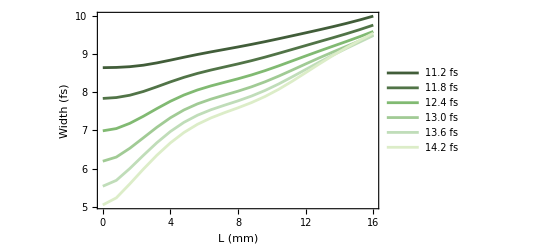

```mathematica
Show[super112CPI,super118CPI,super124CPI,super130CPI,super136CPI,super142CPI ,Axes->False,PlotRangePadding->{{0.5,0.5},{0.1,0.5}},PlotRange->{All,All},Frame-> True,FrameLabel->{{"Width (fs)"," "},{"L (mm)",Row[{"ϵ (",Superscript["fs","2"],")"}]}},FrameStyle->Directive[Black,14],FrameTicks-> {{Automatic, False},{dispXticks2, epsilonXticks2}}]
```

```mathematica
superB112[[2]][[-1]]
superB118[[2]][[-1]]
superB124[[2]][[-1]]
superB130[[2]][[-1]]
superB136[[2]][[-1]]
superB142[[2]][[-1]]
```

9.98972

9.75498

9.5887

9.49664

9.48151

9.54391

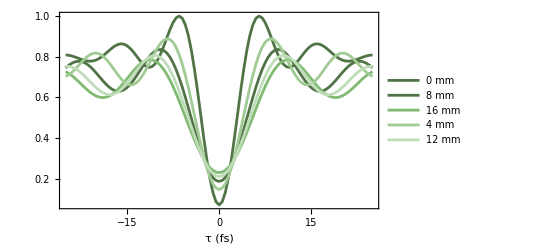

```mathematica
tauList = Table[t, {t,-25.0,25.0,0.5}];
xticks = Table[xt, {xt, 0, 1,0.2}];

superDip0mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip4mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_4000.txt", "List"];
superDipmax4= Max[superDip4mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip4mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["4 mm",20]}];

superDip12mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_12000.txt", "List"];
superDipmax5= Max[superDip12mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip12mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{" ","Intensity (arb)"},{"τ (fs) ", "b=1.42 "}},FrameStyle->Directive[Black,24], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

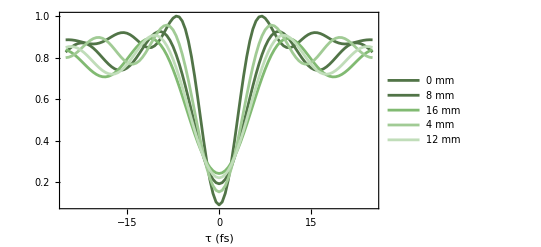

```mathematica
superDip0mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip4mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\dip_4000.txt", "List"];
superDipmax4= Max[superDip4mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip4mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["4 mm",20]}];

superDip12mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\dip_12000.txt", "List"];
superDipmax5= Max[superDip12mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip12mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{" ","Intensity (arb)"},{"τ (fs) ", "b= 1.36 "}},FrameStyle->Directive[Black,24], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

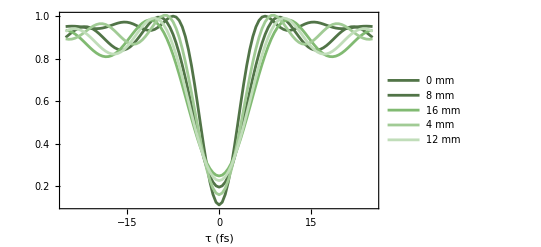

```mathematica
superDip0mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip4mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\dip_4000.txt", "List"];
superDipmax4= Max[superDip4mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip4mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["4 mm",20]}];

superDip12mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\dip_12000.txt", "List"];
superDipmax5= Max[superDip12mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip12mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{" ","Intensity (arb)"},{"τ (fs) ", "b= 1.30"}},FrameStyle->Directive[Black,24], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

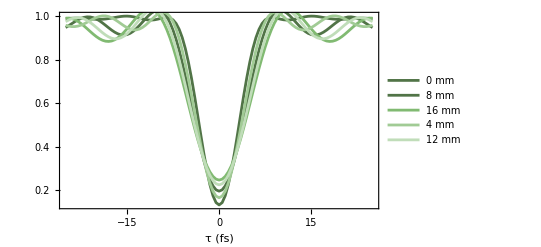

```mathematica
superDip0mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip4mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\dip_4000.txt", "List"];
superDipmax4= Max[superDip4mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip4mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["4 mm",20]}];

superDip12mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\dip_12000.txt", "List"];
superDipmax5= Max[superDip12mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip12mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{" ","Intensity (arb)"},{"τ (fs) ", "b=1.24 "}},FrameStyle->Directive[Black,24], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

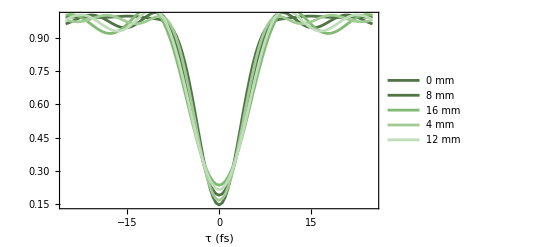

```mathematica
superDip0mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip4mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\dip_4000.txt", "List"];
superDipmax4= Max[superDip4mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip4mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["4 mm",20]}];

superDip12mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\dip_12000.txt", "List"];
superDipmax5= Max[superDip12mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip12mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{" ","Intensity (arb)"},{"τ (fs) ", "b= 1.18 "}},FrameStyle->Directive[Black,24], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

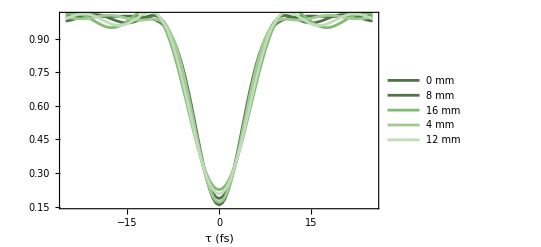

```mathematica
superDip0mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip4mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\dip_4000.txt", "List"];
superDipmax4= Max[superDip4mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip4mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["4 mm",20]}];

superDip12mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\dip_12000.txt", "List"];
superDipmax5= Max[superDip12mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip12mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{" ","Intensity (arb)"},{"τ (fs) ", "b=1.12 "}},FrameStyle->Directive[Black,24], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

FindMinimum::nrnum: The function value False is not a real number at {a1,a2,T0,a3,σFWHM} = {-33.9679,0.478211,-0.0538621,-69.2528,-13.414}.

{0.0000183379,{a1→0.00474155,a2→1.74376×10^-6,T0→0.001,a3→0.899999,σFWHM→7.}}

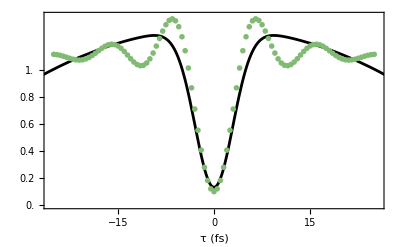

```mathematica
superDip0mm42 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_0.txt", "List"];
superDipmax = Max[superDip0mm];
fitfunc[t_]:= (a1 - a2*(t-T0)^2)*(1 -a3* Exp[-4*Log[2]*(t-T0)^2/(σFWHM^2)])
Chisq = Sum[(superDip0mm42[[i]]-fitfunc[tauList[[i]]])^2,{i,1,Length[tauList]}];
fitvals=FindMinimum[{Chisq&&σFWHM>0},{{a1,0.0025},{a2,0.00000001},{T0,0.001},{a3,0.9},{σFWHM,7}}]
pfit3=Quiet[Plot[fitfunc[t]/superDipmax/.{fitvals[[2]]},{t,-300,300},PlotRange->{{-25.5,25.5},{0,1.4}}, PlotStyle->Black,AxesOrigin->{-25.5,0}]];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm42[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#81BA72"],PointSize[0.01]}];
Show[pfit3,superDipPlot,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{"τ (fs)"," "},FrameStyle->Directive[Black,14], FrameTicks->{{xticks,True},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

{8.57194×10^-6,{a1→0.0044504,a2→1.02413×10^-6,T0→-8.04691×10^-16,a3→0.967724,σFWHM→5.05243}}

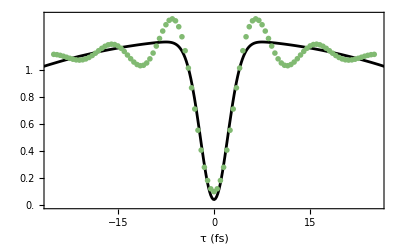

```mathematica
superDip0mm42 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_0.txt", "List"];
superDipmax = Max[superDip0mm];
fitfunc[t_]:= (a1 - a2*(t-T0)^2)*(1 -a3* Exp[-4*Log[2]*(t-T0)^2/(σFWHM^2)])
Chisq = Sum[(superDip0mm42[[i]]-fitfunc[tauList[[i]]])^2,{i,1,Length[tauList]}];
fitvals=FindMinimum[Chisq,{{a1,0.0025},{a2,0.00000001},{T0,0.001},{a3,0.9},{σFWHM,7}}]
pfit3=Quiet[Plot[fitfunc[t]/superDipmax/.{fitvals[[2]]},{t,-300,300},PlotRange->{{-25.5,25.5},{0,1.4}}, PlotStyle->Black,AxesOrigin->{-25.5,0}]];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip0mm42[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#81BA72"],PointSize[0.01]}];
Show[pfit3,superDipPlot,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{"τ (fs)"," "},FrameStyle->Directive[Black,14], FrameTicks->{{xticks,True},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

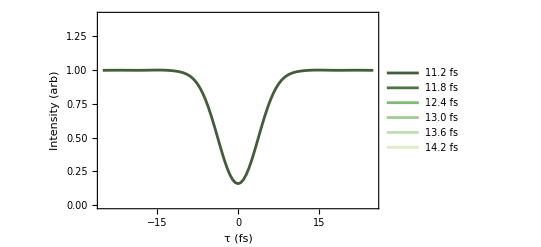

```mathematica
superDip0mm1 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_142\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm6];
superDipPlot1 =ListPlot[Table[{ tauList[[i]],superDip0mm1[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#DCEDC8"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "14.2 fs"}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["14.2 fs",16]}];

superDip0mm2 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_136\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm6];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip0mm2[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "13.6 fs"}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["13.6 fs",16]}];

superDip0mm3 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_130\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm6];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip0mm3[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "13.0 fs"}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["13.0 fs",16]}];

superDip0mm4 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_124\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm6];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip0mm4[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "12.4 fs"}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["12.4 fs",16]}];

superDip0mm5 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_118\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm6];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip0mm5[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "11.8 fs"}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["11.8 fs",16]}];

superDip0mm6 = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\super duper erf\\march18 results\\B_112\\dip_0.txt", "List"];
superDipmax= Max[superDip0mm6];
superDipPlot6 =ListPlot[Table[{ tauList[[i]],superDip0mm6[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#415D39"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "11.2 fs"}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["11.2 fs",16]}];

Show[superDipPlot6, superDipPlot5, superDipPlot4, superDipPlot3, superDipPlot2,superDipPlot1,Axes->False,PlotRange->{All,{0,1.4}}, PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity (arb)"," "},{"τ (fs) ", "ϵ = 0 "}},FrameStyle->Directive[Black,16], FrameTicks->{{True,xticks},{True,True}},FrameTicksStyle->{{Automatic,FontSize->0},{Automatic,Automatic}}]
```

{{0,0},{16000,16},{32000,32},{48000,48},{64000,64}}

{{0.,0},{13438.6,300},{26877.1,600},{40315.7,900},{53754.2,1200}}

{{0,0},{200,200},{400,400},{600,600},{800,800}}

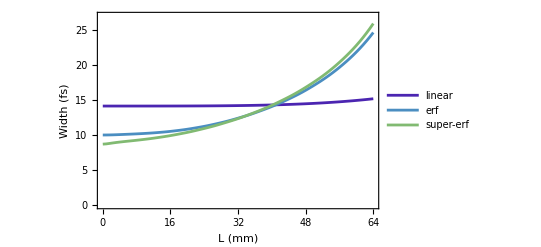

```mathematica
lindata = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\linear_0_64_mar7.txt", "CSV"]];
erfdata = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_0_64_mar7.txt", "CSV"]];
erfsuperdata = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_0_64_mar7.txt", "CSV"]];
dispXticks2= Table[{i*1000,i},{i,0,64,16}]
testingTicks = Table[{i/0.02232382460030012,i},{i,0,1428,300}]
widthTicks = Table[{i,i},{i,0,800,200}]
Lvalues = Table[ϵ/0.02232382460030012, {ϵ,0,1428}];
linCPI = ListPlot[Table[{ lindata[[1]][[i]],lindata[[2]][[i]]}, {i, 1 , Length[lindata[[1]]]}], PlotRange->{All,All}, Joined->True, PlotStyle->RGBColor["#4B25B1"],PlotLegends->{Style["linear",14]}];
erfCPI = ListPlot[Table[{ erfdata[[1]][[i]],erfdata[[2]][[i]]}, {i, 1 , Length[erfdata[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->RGBColor["#4B8EC1"],PlotLegends->{Style["erf",14]}];
erfsuperCPI = ListPlot[Table[{ erfsuperdata[[1]][[i]],erfsuperdata[[2]][[i]]}, {i, 1 , Length[erfsuperdata[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->RGBColor["#81BA72"],PlotLegends->{Style["super-erf",14]}];

Show[linCPI, erfCPI, erfsuperCPI, PlotRangePadding->{{0.5,0.5},{0.1,0.5}},PlotRange->{All,{0,27}},Frame-> True,FrameLabel->{{"Width (fs)"," "},{"L (mm)",Row[{"ϵ (",Superscript["fs","2"],")"}]}},FrameStyle->Directive[Black,16],FrameTicks-> {{Automatic, False},{dispXticks2, testingTicks}}, Axes->False]
```